```mathematica
(*  Checking the existence of the 5-chromatic 972-vertex unit distance graph
embedded in the circumsphere of the great icosahedron with unit edge lengths. 
Vsevolod Voronov, Anna Neopryatnaya, Eugene Dergachev 
  e-mail: v-vor@yandex.ru        *)

(*  requires IGraph/M: https://github.com/szhorvat/IGraphM  *)

(* code from this page 
https://mathandcode.com/2016/06/06/polyhedramathematica.html 
 is used to generate symmetry group *)

(* Numerically check if a square matrix is the identity matrix to within some accuracy *)
isIdentityMatrix[r_]:=(Flatten[N[r-IdentityMatrix[Length[r]]]].Flatten[N[r-IdentityMatrix[Length[r]]]]<0.001);

(* Numerically check if any matrix is the zero matrix to within some accuracy *)
isZeroMatrix[r_]:=(Flatten[N[r]].Flatten[N[r]]<0.00001);

(* Numerically test and remove duplicate matrices from a list *)
reduce[list_]:=Union[list,SameTest->(isZeroMatrix[#1-#2]&)];

(* Given a list of square matrices g, this function combines all possible pairs of matrices in all possible orders, and numerically removes all duplicate matrices *)
iterate[g_]:=reduce[FullSimplify[#1.#2]&@@@Tuples[g,2]];

(* Given a generating set of matrices, this function creates a group. If the generators aren't actually a generating set, 
this code runs forever! *)
makeGroup[generators_]:=FixedPoint[iterate,Join[generators,{IdentityMatrix[3]}]];

orbit[point_,group_]:=reduce[#.point&/@group];

(* computing the adjacence matrix of the distance graph *)
(* it's better to check distances numerically before the analytic computation  *)
DistOne[i_,j_]:= (Abs[(Nvertices[[i]]-Nvertices[[j]]).(Nvertices[[i]]-Nvertices[[j]])-1]<0.00000001&& FullSimplify[Sum[(vertices[[i]][[k]]-vertices[[j]][[k]])^2,{k,1,3}]]==1);

DistOneN[i_,j_]:= (Abs[(Nvertices[[i]]-Nvertices[[j]]).(Nvertices[[i]]-Nvertices[[j]])-1]<0.00000001);

UnitDist[L_]:= Boole[DistOne[#1,#2]&@@@Subsets[L,{2}]];
```

```mathematica
(* icosahedron symmetry group elements*)
f=(1+Sqrt[5])/2;
mirr = {{1,0,0},{0,0,1},{0,1,0}};
icoGenerators={{{-1,0,0},{0,-1,0},{0,0,1}},{{0,0,1},{1,0,0},{0,1,0}},mirr.(1/2 {{1,-f,1/f},{f,1/f,-1},{1/f,1,f}}).mirr,{{1,0,0},{0,-1,0},{0,0,1}}};


icoG=makeGroup[icoGenerators];
```

```mathematica
(*  vertex of the icosahedron  *)
v= {1/2,(Sqrt[5]+1)/4,0}/f;

(* using 8 points from the embedding of the 10-vertex unit distance graph 
  we compute 8*120 vertices  *)

v11 = Root[-49-147 #1-71 #1^2+67 #1^3+129 #1^4+97 #1^5+42 #1^6+10 #1^7+#1^8&,2]/2;
v12 = Root[-19+57 #1+206 #1^2+117 #1^3-11 #1^4-23 #1^5+#1^6+2 #1^7+#1^8&,1]/2;
v13 = Root[25+150 #1+315 #1^2+370 #1^3+284 #1^4+145 #1^5+49 #1^6+10 #1^7+#1^8&,2]/2;
v21= Root[-49-147 #1-71 #1^2+67 #1^3+129 #1^4+97 #1^5+42 #1^6+10 #1^7+#1^8&,1]/2;
v22= Root[-19+57 #1+206 #1^2+117 #1^3-11 #1^4-23 #1^5+#1^6+2 #1^7+#1^8&,2]/2;
v23=-Root[25+150 #1+315 #1^2+370 #1^3+284 #1^4+145 #1^5+49 #1^6+10 #1^7+#1^8&,1]/2 ;
v31=Root[1+#1-16 #1^2-21 #1^3+34 #1^4+156 #1^5+234 #1^6+159 #1^7+41 #1^8&,1]/2 ;
v32= Root[-1-15 #1-55 #1^2-121 #1^3+269 #1^4+690 #1^5+616 #1^6+257 #1^7+41 #1^8&,1]/2;
v33= Root[-41-211 #1-231 #1^2-148 #1^3-13 #1^4+75 #1^5+223 #1^6+174 #1^7+41 #1^8&,1]/2;
v41 = Root[1+#1-16 #1^2-21 #1^3+34 #1^4+156 #1^5+234 #1^6+159 #1^7+41 #1^8&,2]/2;
v42 =- Root[-1-15 #1-55 #1^2-121 #1^3+269 #1^4+690 #1^5+616 #1^6+257 #1^7+41 #1^8&,2]/2;
v43 = -Root[-41-211 #1-231 #1^2-148 #1^3-13 #1^4+75 #1^5+223 #1^6+174 #1^7+41 #1^8&,2]/2;
v51= Root[-1+5 #1+10 #1^2+8 #1^3+69 #1^4+205 #1^5+269 #1^6+169 #1^7+41 #1^8&,2]/2;
v52=Root[1-13 #1+61 #1^2-138 #1^3+164 #1^4-118 #1^5+96 #1^6-93 #1^7+41 #1^8&,2]/2;
v53=Root[269-232 #1-669 #1^2+471 #1^3+642 #1^4-335 #1^5-258 #1^6+72 #1^7+41 #1^8&,2]/2;
v61=Root[-1+5 #1+10 #1^2+8 #1^3+69 #1^4+205 #1^5+269 #1^6+169 #1^7+41 #1^8&,1]/2;
v62=Root[1-13 #1+61 #1^2-138 #1^3+164 #1^4-118 #1^5+96 #1^6-93 #1^7+41 #1^8&,1]/2;
v63=Root[269+232 #1-669 #1^2-471 #1^3+642 #1^4+335 #1^5-258 #1^6-72 #1^7+41 #1^8&,2]/2;
v71 = Root[-1+4 #1-2 #1^2-12 #1^3-#1^4+15 #1^5+15 #1^6+6 #1^7+#1^8&,1]/2;
v72 = Root[-1+10 #1-5 #1^2+18 #1^3+19 #1^4-15 #1^5-#1^6-#1^7+#1^8&,2]/2;
v73 = Root[1-14 #1+36 #1^2+29 #1^3+13 #1^4+17 #1^5+19 #1^6+7 #1^7+#1^8&,1]/2;
v81=Root[-1-#1-2 #1^2+4 #1^3+14 #1^4+15 #1^5+13 #1^6+6 #1^7+#1^8&,1]/2;
v82=1/2 (1-√(6-3 √5+2 √(-37/2+(17 √5)/2)))/2;
v83=Root[-41-37 #1+108 #1^2+45 #1^3-42 #1^4-11 #1^5+4 #1^6+2 #1^7+#1^8&,2]/2;


(*  although equations can be solved explicitely, it's more efficient to express the solutions by Root[] objects *)

vect={{v11,v12,v13},{v21,v22,v23},{v31,v32,v33},{v41,v42,v43},{v51,v52,v53},{v61,v62,v63},{v71,v72,v73},{v81,v82,v83}};
nVect=8;
nVer = 972;
```

```mathematica
icosV=orbit[v,icoG];
vertices={};
For[i=1,i≤nVect,i++, vertices=Join[vertices,FullSimplify[orbit[vect[[i]],icoG]]];Print[Length[vertices]]];
vertices=Join[vertices,icosV];


(* here coordinates of all 372 vertices are represented by Root[] objects *)

Length[vertices]

(* number of vertices *)
```

120

240

360

480

600

720

840

960

972

```mathematica
ind=Range[972];
(* pairs of vertices *)
LS = Subsets[ind,{2}];

(* numerical form is required to speed up *)
Nvertices=N[vertices, 10];


(* --------------------------------this step consumes most of the time ------------------------------------ *)
(* the numerical-only computation (DistOneN) is much faster, but it doesn't make any sense as a proof -----------*)

AdjMatr = Parallelize[Boole[DistOne[#1,#2]&@@@LS]];

(* ----------------------------- 10-30 min depending of CPU speed -----------------------------------------*)

Total[AdjMatr]

(* number of edges *)
```

4110

```mathematica
ListPointPlot3D[Nvertices]
```

-Graphics3D-

```mathematica
edges={};
For[i=1,i≤Length[LS],i++,If[AdjMatr[[i]]==1,AppendTo[edges,LS[[i]]],]];
Length[edges]
```

4110

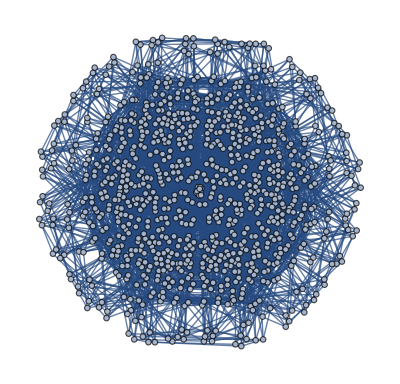

```mathematica
g = Graph[edges]
```

```mathematica
<<IGraphM`
```

IGraph/M 0.3.112 (May 7, 2019)

Evaluate IGDocumentation[] to get started.

```mathematica
IGChromaticNumber[g]
```

5